1

1th iteration value is :3/2

Estimated error in1th iteration is: 1/2

2th iteration value is :5/4

Estimated error in2th iteration is: 1/4

3th iteration value is :11/8

Estimated error in3th iteration is: 1/8

4th iteration value is :21/16

Estimated error in4th iteration is: 1/16

The appropriate root is: 1.3125

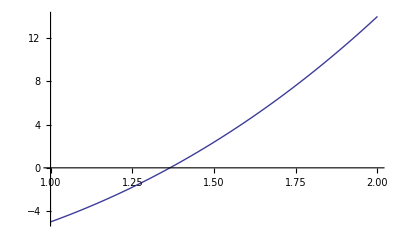

```mathematica
f[x_]:= x^3 + 4 *x^2 - 10
a=1
b=2;
epsilon = 0.01;
Nmax = 5;
If[f[a]*f[b]>0,
Print["Theres values do not satisfy the IVP so change the initial value"],
 For[i = 1, i<Nmax,i++,c=(a+b)/2;
	If [Abs[(b-a)/2]<epsilon, Return[c],
	Print[i,"th iteration value is :",c];
	Print["Estimated error in",i,"th iteration is: ",(b-a)/2];
If [f[a]*f[c]<0,b=c,a=c]]]];
Print["The appropriate root is: ", N[c]];
Plot[f[x],{x,1,2}]
```